```mathematica
(* local Weyl operators *)
Clear[v,u,p,n]
p=5;
ω=ⅇ^(ⅈ*(2π)/p);
v = ConstantArray[0,{p,p}];
u = ConstantArray[0,{p,p}];
Do[
If[n+1≤p,
v[[n,n+1]]=1;
,
v[[p,1]]=1;
];
u[[n,n]]=ω^(n-1)
,{n,p}];
v=SparseArray[v];
u=SparseArray[u];
MatrixForm[v]
MatrixForm[u]
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0
0 | ⅇ^((2 ⅈ π)/5) | 0 | 0 | 0
0 | 0 | ⅇ^((4 ⅈ π)/5) | 0 | 0
0 | 0 | 0 | ⅇ^(-(4 ⅈ π)/5) | 0
0 | 0 | 0 | 0 | ⅇ^(-(2 ⅈ π)/5))

```mathematica
Clear[linkVals]
linkVals[ϕ_] = Refine[Eigenvalues[ⅇ^(ⅈ ϕ)*v.(v.u)†+ⅇ^(-ⅈ ϕ)*(v.u).v†],ϕ>0]//FullSimplify
```

{2 Cos[ϕ],(-1)^(1/5) ⅇ^(-ⅈ ϕ) ((-1)^(3/5)-ⅇ^(2 ⅈ ϕ)),-(-1)^(3/5) ⅇ^(-ⅈ ϕ) ((-1)^(4/5)+ⅇ^(2 ⅈ ϕ)),(-1)^(1/5) ⅇ^(-ⅈ ϕ) (-1+(-1)^(3/5) ⅇ^(2 ⅈ ϕ)),(-1)^(2/5) ⅇ^(-ⅈ ϕ) (-(-1)^(1/5)+ⅇ^(2 ⅈ ϕ))}

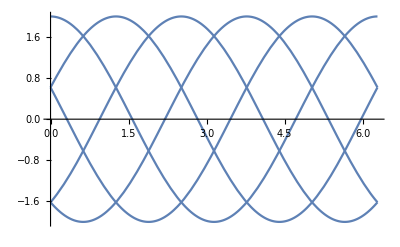

```mathematica
Plot[linkVals[ϕ],{ϕ,0,2π}]
```

```mathematica
(* give them a string for nonlocal commutation relations *)
Clear[L,V,U]
L=3;
Do[
V[i]=KroneckerProduct[IdentityMatrix[p^(i-1)],v,IdentityMatrix[p^(L-i)]];
U[i]=KroneckerProduct[IdentityMatrix[p^(i-1)],u,IdentityMatrix[p^(L-i)]];

Γ[i]=If[i>1,V[i].∏_(j=1)^(i-1) U[j],V[i]];
Δ[i]=Γ[i].U[i];

,{i,1,L}];
```

```mathematica
spectrum={};
ϕs={};
Do[
h=0.0;
J=1*ⅇ^(ⅈ ϕ);
HVP = -h*(∑_(i=1)^L Γ[i]†.Δ[i])-J*(∑_(i=1)^(L-1) Δ[i].Γ[i+1]†);
HVP=HVP+HVP†;
{evals,evecs}=Eigensystem[Normal[HVP]];
evals=Tally[evals/Max[(L-1),1],Abs[#1-#2]<10^-6&];
AppendTo[spectrum,evals];
AppendTo[ϕs,ϕ/π];
,{ϕ,π/31,2π,π/33}]
```

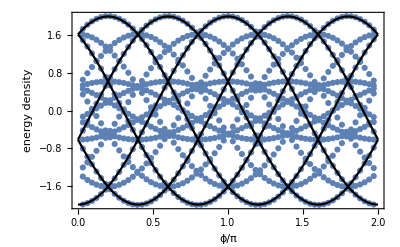

```mathematica
min=Min[Table[Length@ss,{ss,spectrum}]];
pmax=Max[Partition[Flatten[spectrum],2][[All,1]]];
pmin=Min[Partition[Flatten[spectrum],2][[All,1]]];
Show[Table[{ϕs,spectrum[[All,i,1]]}ᵀ//ListPlot,{i,min}],Plot[Table[-2Re[J] Cos[π(x-2n/p)],{n,0,p-1}],{x,0,2},PlotStyle->Black],PlotRange->{pmin,pmax},GridLines->{Table[i/p,{i,2p}],{}},Frame->True,FrameLabel->{"ϕ/π","energy density"}]
```

```mathematica
(* check all local commutation relations *)
test={};
Do[
tp=SparseArray[Γ[i].Γ[j]-ω*Γ[j].Γ[i]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];

tp=SparseArray[Γ[j].Γ[i]-ω**Γ[i].Γ[j]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];

tp=SparseArray[Δ[i].Δ[j]-ω*Δ[j].Δ[i]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];

tp=SparseArray[Δ[j].Δ[i]-ω**Δ[i].Δ[j]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];

,{j,L},{i,j-1}]
Do[
tp=SparseArray[Γ[i].Δ[j]-ω*Δ[j].Γ[i]]//ArrayRules;
If[tp!={{_,_}->0},AppendTo[test,tp];];
,{j,L},{i,j}];
test
```

{}